```mathematica
Quit
```

Local process id:

```mathematica
$ProcessID
```

12468

#### Common Settings

Host and port:

```mathematica
host="18.217.160.48";
port="80";
```

#### GET

With GET:

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->"GET"|>,{$ProcessID,$MachineName}]
```

{7186,ip-172-31-39-91}

#### POST

```mathematica
method="POST";
```

With POST and BASE64:

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,{$ProcessID,$MachineName}]//AbsoluteTiming
```

{0.226906,{7186,ip-172-31-39-91}}

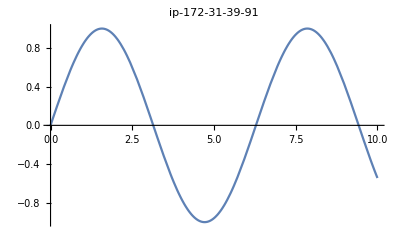
{0.355861,-Graphics-}

```mathematica
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,Plot[Sin[x],{x,0,10},PlotLabel->$MachineName]]//AbsoluteTiming
```

```mathematica
Manipulate[
With[{a=a},
EvaluationRequest[<|"Host"->host,"Port"->port,"Method"->method,"Encoding"->"Base64"|>,Plot[Sin[a x],{x,0,10},PlotLabel->$MachineName,Filling->Axis]]],{a,1,10},ContinuousAction->False]
```